## public

```mathematica
BeginPackage["MusicNotation`"]
```

MusicNotation`

### messages

#### usage

```mathematica
DisplayScore::usage="Creates a visual score.";
```

```mathematica
ReadScoreFile::usage="Read and validate a music file. The file should have an .rmn extension and use the rmn notation.";
```

```mathematica
ReadScore::usage="Read and validate a string representation of a score written in the rmn notation.";
```

```mathematica
EmptyVoice::usage="A representation of a voice that contains no music information.";
```

```mathematica
EmptyScore::usage="A score representation with no music information.";
```

```mathematica
Score::usage="A representation of a musical score. Use ReadScore or ReadScoreFile to create a Score from the rmn notation.";
```

```mathematica
ScoreInformation::usage="Meta information about the score.";
```

```mathematica
Voice::usage="A container for all of the measures in a score pertaining to one of its voices.";
```

```mathematica
Measure::usage="A representation of on measure of music in a score.";
```

```mathematica
Chord::usage="A representation of a collection of notes.";
```

```mathematica
Silence::usage="A representation of a rest.";
```

```mathematica
Sustain::usate="A representation of a sustain.";
```

#### errors

```mathematica
ReadScoreFile::bad extension="Unrecognized extension in filename `1`";
ReadScoreFile::no file exists="No file exists for `1`";
```

## private

```mathematica
Begin["rmn`"]
```

rmn`

### constants

```mathematica
IgnoreDelimiters={"\n"};
LineDelimiters={"\n"};
MeasureDelimiters={"|"};
VoiceIndicator="~";
NoteRE="[abcdefgABCDEFG]";
OctaveRE="\\d?";
AccidentalRE="[+-]?";
RestRE="#|_";
SustainRE="\\.";
VoiceRE="(?m)^(~.*$)?[^~@]*";
VoiceNameRE="(?m)^~+(.*)";
InformationRE="(?m)^@.*$";
InformationPairRE="@([^:]+):(.*)";
MeasureLineRE="(?m)^[^~].*$";
```

### core model

```mathematica
BaseNoteValue["c"]:=0;
BaseNoteValue["d"]:=2;
BaseNoteValue["e"]:=4;
BaseNoteValue["f"]:=5;
BaseNoteValue["g"]:=7;
BaseNoteValue["a"]:=9;
BaseNoteValue["b"]:=11;
```

```mathematica
BaseNoteValue["C"]:=-12;
BaseNoteValue["D"]:=-10;
BaseNoteValue["E"]:=-8;
BaseNoteValue["F"]:=-7;
BaseNoteValue["G"]:=-5;
BaseNoteValue["A"]:=-3;
BaseNoteValue["B"]:=-1;
```

```mathematica
OctaveSign["A"|"B"|"C"|"D"|"E"|"F"|"G"]:=-1;
OctaveSign["a"|"b"|"c"|"d"|"e"|"f"|"g"]:=+1;
```

### helpers

```mathematica
MeasurePatternQ[s_String]:=!InformationPatternQ[s];
```

```mathematica
InformationPatternQ[s_String]:=StringMatchQ[s,RegularExpression["^@.+$"]];
```

```mathematica
SustainQ[n_String]:=StringMatchQ[n,RegularExpression[SustainRE]];
```

```mathematica
RestQ[n_String]:=StringMatchQ[n,RegularExpression[RestRE]];
```

```mathematica
Chord[]:=Silence[];
```

```mathematica
EmptyInformation[]:=ScoreInformation[];
```

```mathematica
EmptyMeasure[]:=Measure[];
```

```mathematica
EmptyVoice[]:=Voice["",{EmptyMeasure[]}];
```

```mathematica
EmptyScore[]:=Score[EmptyInformation[],{EmptyVoice[]}];
```

### parsers

```mathematica
ToLines[data_]:=StringSplit[data,LineDelimiters];
```

```mathematica
ToMeasureData[data_]:=StringSplit[data,MeasureDelimiters,All];
```

```mathematica
ToChordData[mdata_]:=StringSplit[mdata];
```

```mathematica
ToNote[ndata_]:=ToNote[Characters[ndata]];
ToNote[{n_?SustainQ,___}]:=Sustain[];
ToNote[{n_?RestQ,___}]:=Silence[];
ToNote[{n_}]:=BaseNoteValue[n];
ToNote[{n__,"+"}]:=1+ToNote[{n}];
ToNote[{n__,"-"}]:=-1+ToNote[{n}];
ToNote[{n_,o_}]:=12 OctaveSign[n] ToExpression[o]+BaseNoteValue[n];
```

```mathematica
ToChord[notes_]:=Chord@@ToNote/@StringCases[notes,RegularExpression["("<>SustainRE<>")|("<>RestRE<>")|("<>NoteRE<>OctaveRE<>AccidentalRE<>")"]]
```

```mathematica
ToMeasure[chords:{___}]:=Measure@@MapIndexed[{First[(#2-1)/Length@chords],#1}&,chords];
ToMeasure[mdata_String]:=ToMeasure[ToChord/@ToChordData[mdata]];
```

```mathematica
ToInformationItem["date",v_]:=Rule["date",DateObject[v]];
ToInformationItem[k_,v_]:=Rule[k,v];
```

```mathematica
ToInformation[{}]:=EmptyInformation[];
ToInformation[infos_]:=ScoreInformation[Association[StringCases[#,RegularExpression[InformationPairRE]:>ToInformationItem["$1","$2"]]&/@infos]];
```

```mathematica
ToVoice[""]:=EmptyVoice[];
ToVoice[vdata_]:=
With[
{
voiceNameMaybe=StringCases[vdata,RegularExpression[VoiceNameRE]->"$1"],
measureLines=StringCases[vdata,RegularExpression[MeasureLineRE]]
},
Voice[If[0==Length@voiceNameMaybe,"~anonymous voice~",First@voiceNameMaybe],ToMeasure/@Flatten[ToMeasureData[measureLines]]]
];
```

### transformers

```mathematica
ReadScoreFile[scoreFile_]:=
Which[
"rmn"!=FileExtension[scoreFile],Message[ReadScoreFile::bad extension,FileNameTake[scoreFile]];EmptyScore[],
FileExistsQ[scoreFile],ReadScore[ReadString[scoreFile]],
True,Message[ReadScoreFile::no file exists,scoreFile];EmptyScore[]
];
```

```mathematica
ReadScore[score_String]:=
With[
{
information=StringCases[score,RegularExpression[InformationRE]],
voices=StringCases[StringTrim[StringReplace[score,RegularExpression[InformationRE]->""]],RegularExpression[VoiceRE]]
},
Score[ToInformation[information],ToVoice/@StringTrim/@voices]
];
```

### accessors

```mathematica
Voices[EmptyScore[]]={};
Voices[score_Score]:=score[[2]];
```

```mathematica
Measures[{}]={};
Measures[voice_Voice]:=voice[[2]];
```

### display

```mathematica
MeasureStaffElements[lineThickness_,lineWidth_,measureWidth_]:=
{GrayLevel[.5],Thickness[lineThickness],Line[{{-lineWidth/2,-3},{-lineWidth/2,14}}],Line[{{measureWidth+lineWidth/2,-3},{measureWidth+lineWidth/2,14}}],Line[{{0,2},{10,2}}],Line[{{0,4},{10,4}}],Line[{{0,5},{10,5}}],Line[{{0,7},{10,7}}],Line[{{0,9},{10,9}}]};
```

```mathematica
ChordElements[measureWidth_][{hor_,Chord[notes___]}]:=Disk[{.5+hor measureWidth,#},.5]&/@{notes};
ChordElements[measureWidth_][{hor_,Silence[___]}]:={Red,Rectangle[{hor measureWidth,4.5},{1+hor measureWidth,6.5}]};
```

```mathematica
MeasureElements[measureWidth_,colorFn_][Measure[chords___],{voiceNum_}]:=
{colorFn[voiceNum],ChordElements[measureWidth]/@{chords}};
```

```mathematica
DisplayMeasure[lineThickness_,lineWidth_,measureWidth_,colorFn_][mvoices:{___Measure}]:=
Graphics[{MeasureStaffElements[lineThickness,lineWidth,measureWidth],MapIndexed[MeasureElements[measureWidth,colorFn],mvoices]}];
```

```mathematica
DisplayScore[score_String]:=DisplayScore[ReadScore[score]];
DisplayScore[score_Score]:=
With[
{
measureWidth=10,
measureCount=Max[Length[Measures[#]]&/@Voices[score],0],
lineWidth=.5,
colorFn=Function[n,If[OddQ[n],Black,Green]]
},
With[
{
lineThickness=lineWidth/(2 lineWidth+measureWidth)
},
DisplayMeasure[lineThickness,lineWidth,measureWidth,colorFn]/@Transpose[Replace[PadRight[Measures/@Voices[score]],0->EmptyMeasure[],{2}]]
]
];
```

## end

```mathematica
End[]
```

rmn`

```mathematica
EndPackage[]
```

## test

```mathematica
PadRight[{{a,b,c},{d}}]/.(0->EmptyMeasure[])
```

{{a,b,c},{d,EmptyMeasure[],EmptyMeasure[]}}

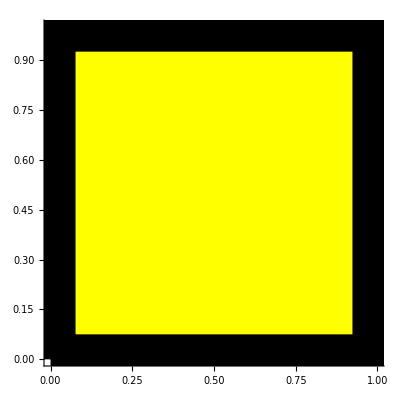

```mathematica
Graphics[{EdgeForm[{Black,Thickness[.09]}],FaceForm[Yellow],Rectangle[]},Axes->True,PlotRange->{{0,1},{0,1}},PlotRangeClipping->True]
```

```mathematica
StringSplit["|","|",All]
```

{,}

```mathematica
s=ReadString[FileNameJoin[{NotebookDirectory[],"TestData","twoVoices.rmn"}]]
```

-one
c d e f g a b c1
--two
G A B c d e f+ g

```mathematica
StringCases[s,RegularExpression["^@.+$"]]
```

{}

```mathematica
"-\n-\n"
```

-
-

```mathematica
StringCases["@key:C\n@composer:me\n\n-\n",RegularExpression["(?m)^@.*$"]]
```

{@key:C,@composer:me}

```mathematica
s
```

-one
c d e f g a b c1
--two
G A B c d e f+ g

```mathematica
StringCases[s,RegularExpression["(?m)^(-.*$)?[^-@]*"]]
```

{-one
c d e f g a b c1
,--two
G A B c d e f+ g
,}

```mathematica
StringCases[s,StartOfLine~~"-"~~Except["\n"]...]//FullForm
```

List["-one","--two"]